# Risk Reduction

## Monte Carlo of Sampling Error of Placebo

I did not know you can use the Bernoulli’s distribution and run a Monte Carlo of how sampling error.

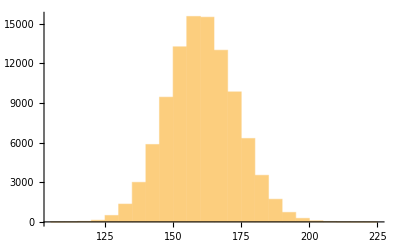

```mathematica
Table[RandomVariate[BernoulliDistribution[160/27000],27000] // Total,{10^5}]//Histogram
```

## Odds Ratio of Sampling Error

One can compute the odds ratio to compare with the vaccine versus without the vaccine with consideration of the sampling error.

```mathematica
ta=Table[1/((RandomVariate[BernoulliDistribution[160/27000],27000]//Total)/(RandomVariate[BernoulliDistribution[8/27000],27000]//Total)),{10^5}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ta//StandardDeviation//N
```

0.0183241

```mathematica
value = ta//Mean //N
```

0.0503112

Odds ratio, you are 20 times more likely to be correct by taking the vaccine based on this study.

```mathematica
1/value
```

19.8763

The error is the following, in worse case of two standard deviations, it is about 3 times more likely to be correct by taking the vaccine within 2 s.d. assuming this is normally distributed.
I think, not sure if this interpretation is okay.

```mathematica
1/(0.183241+(0.0503112*2))
```

3.52282

We can plot the histogram of the odds ratio, how many times we are likely to be wrong.

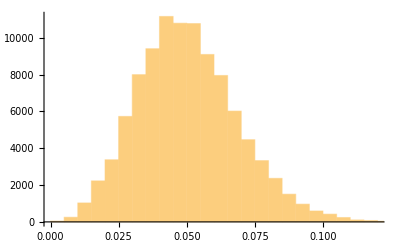

```mathematica
ta//Histogram
```